```mathematica
y[t_] := c(t^2 + 1)^(-2) + t^2 + 1
y'[t] + (4*t/(t^2 +1))* y[t] //Simplify
```

6 t

{1+t^2-4/((1+t^2)^2),1+t^2-2/((1+t^2)^2),1+t^2,1+t^2+4/((1+t^2)^2),1+t^2+2/((1+t^2)^2)}

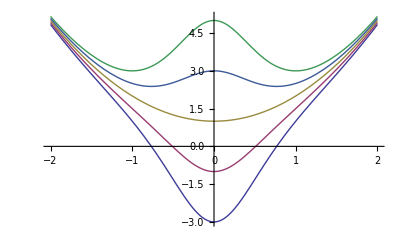

```mathematica
y[t]/. c->{-4, -2, 0, 4, 2}
Plot[ Evaluate [%], {t, -2, 2}]
```

```mathematica
Clear[c]
```

```mathematica
y[t_] := 10 / (1 + c* e^(-t/2))
y'[t] - y[t]/20(10 - y[t]) //Simplify
```

(5 C e^(t/2) (-1+Log[e]))/((C+e^(t/2))^2)

```mathematica
(5 C e^(t/2) (-1+Log[e]))/((C+e^(t/2))^2)

Solve[ y[0] = 2, c]
```

(5 C e^(t/2) (-1+Log[e]))/((C+e^(t/2))^2)

Solve::eqf: 2 is not a well-formed equation.

```mathematica
Solve[2,c]

Solve [ y[0] == 2, c]
```

Solve::eqf: 2 is not a well-formed equation.

Solve[2,c]

{{}}

```mathematica
y[t] = y[t] /. %
Plot [ y[t] , {t, -10, 15}]
```

{10/(1+C e^(-t/2))}

Plot::exclul: {Im[e] - 0} must be a list of equalities or real-valued functions.

-Graphics-